## Nucleation Analysis (Multi - stranded)

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

PartitionFunctionFILE="PartitionFunction_0_0.out";
dPartitionFunctionFILE="dPartitionFunction_0_0.out";
FreeEnergyFILE="FreeEnergy_0_0.out";
dFreeEnergyFILE="dFreeEnergy_0_0.out";
LambdaFILE="mxd_lambda.out";
RoeFILE="mxd_roe.out";
xFILE = "Average_X.out";
yFILE = "Average_Y.out";
zFILE = "Average_Z.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenPATH="collagen/results/";
OtherHarmonic1PATH="collagen_anhar1/results/";
OtherHarmonic2PATH="collagen_anhar2/results/";

FrameBox["Numerical Parameters - Harmonic"] // DisplayForm
PotentialCollagen=Import[CollagenPATH <> PotentialDataFILE,"Table"];
ParametersCollagen=Import[CollagenPATH <>ParametersFILE,"Grid"]
LambdaCollagen=Import[CollagenPATH<>LambdaFILE,"Table"];
RoeCollagen=Import[CollagenPATH<>RoeFILE,"Table"];
xCollagen=Import[CollagenPATH<>xFILE,"Table"];
yCollagen=Import[CollagenPATH<>yFILE,"Table"];
zCollagen=Import[CollagenPATH<>zFILE,"Table"];

FrameBox["Numerical Parameters - Anharmonic 1"] // DisplayForm
PotentialCollagenAnhar1=Import[OtherHarmonic1PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar1=Import[OtherHarmonic1PATH<>ParametersFILE,"Grid"]
LambdaCollagenAnhar1=Import[OtherHarmonic1PATH<>LambdaFILE,"Table"];
RoeCollagenAnhar1=Import[OtherHarmonic1PATH<>RoeFILE,"Table"];
xCollagenAnhar1=Import[OtherHarmonic1PATH<>xFILE,"Table"];
yCollagenAnhar1=Import[OtherHarmonic1PATH<>yFILE,"Table"];
zCollagenAnhar1=Import[OtherHarmonic1PATH<>zFILE,"Table"];

FrameBox["Numerical Parameters - Anharmonic 2"] // DisplayForm
PotentialCollagenAnhar2=Import[OtherHarmonic2PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar2=Import[OtherHarmonic2PATH<>ParametersFILE,"Grid"]
LambdaCollagenAnhar2=Import[OtherHarmonic2PATH<>LambdaFILE,"Table"];
RoeCollagenAnhar2=Import[OtherHarmonic2PATH<>RoeFILE,"Table"];
xCollagenAnhar2=Import[OtherHarmonic2PATH<>xFILE,"Table"];
yCollagenAnhar2=Import[OtherHarmonic2PATH<>yFILE,"Table"];
zCollagenAnhar2=Import[OtherHarmonic2PATH<>zFILE,"Table"];

L=IntegerPart[ParametersCollagen[[1,2]][[2]]];
m=IntegerPart[ParametersCollagen[[1,3]][[2]]];
n=IntegerPart[ParametersCollagen[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagen[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagen[[1,6]][[2]]];

potentialData={PotentialCollagen,PotentialCollagenAnhar1,PotentialCollagenAnhar2};
FreeEnergyData = {FreeEnergyCollagen,FreeEnergyCollagenAnhar1,FreeEnergyCollagenAnhar2};
dFreeEnergyData={dFreeEnergyCollagen,dFreeEnergyCollagenAnhar1,dFreeEnergyCollagenAnhar2};
RoeData={RoeCollagen,RoeCollagenAnhar1,RoeCollagenAnhar2};
LambdaData={LambdaCollagen,LambdaCollagenAnhar1,LambdaCollagenAnhar2};
xData={xCollagen,xCollagenAnhar1,xCollagenAnhar2};
yData={yCollagen,yCollagenAnhar1,yCollagenAnhar2};
zData={zCollagen,zCollagenAnhar1,zCollagenAnhar2};

fsAxesLabel=24;
fs2=18;
fs3=16;

Needs["PlotLegends`"]
```

/homes/ht/Desktop/workspace/collagen_code

Numerical Parameters - Harmonic

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 1

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 2

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

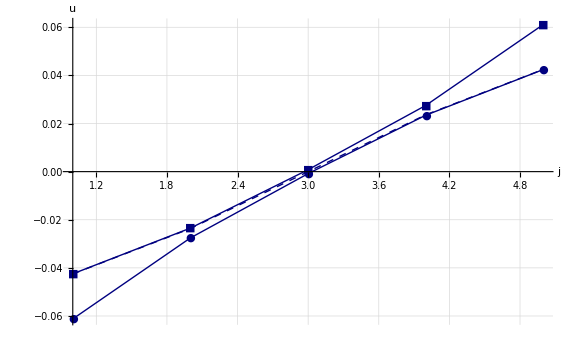
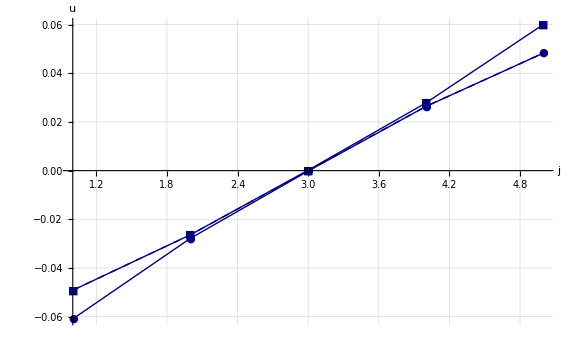
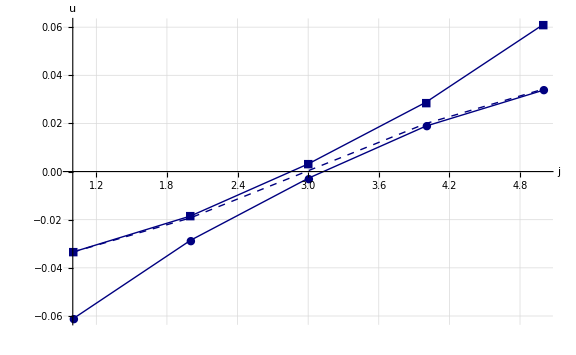

```mathematica
AveragePositionCollagenDataPlot=Table[
ListLinePlot[
{
xData[[i]][[2]],
yData[[i]][[2]],
zData[[i]][[2]]
},
PlotRange->All,
AxesOrigin->{1,0},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["u",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Darker[Blue,0.5]},
{Thick,Dashed,Darker[Blue,0.5]},
{Thick,Darker[Blue,0.5]}
},
PlotMarkers->{"●","","■"},
PlotLegend->{
Style["x_j",FontSize->fs2],
Style["y_j",FontSize->fs2],
Style["z_j",FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.5,0.3},
LegendPosition->{0.4,-0.5}
]
,{i,1,3}
];
AveragePositionCollagenDataPlot
```

```mathematica
Export["./col_avg_har_delta1_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[1]]];
Export["./col_avg_hard_soft_delta1_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[2]]];
Export["./col_avg_soft_hard_delta1_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[3]]];
```

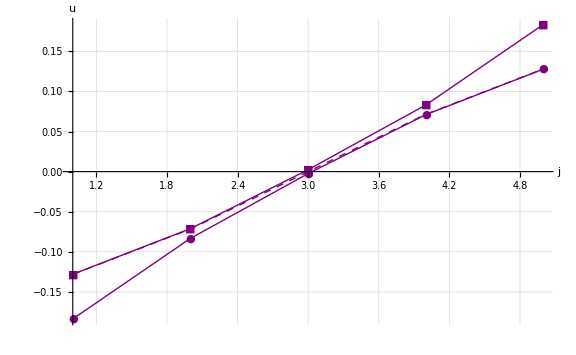
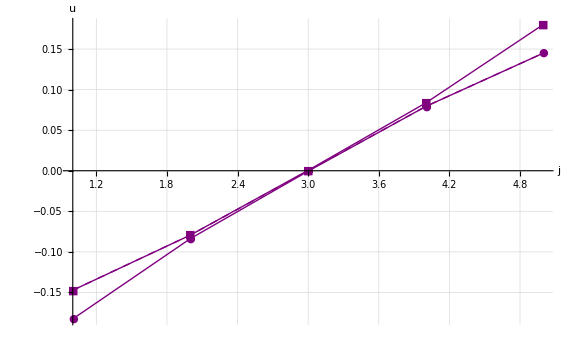
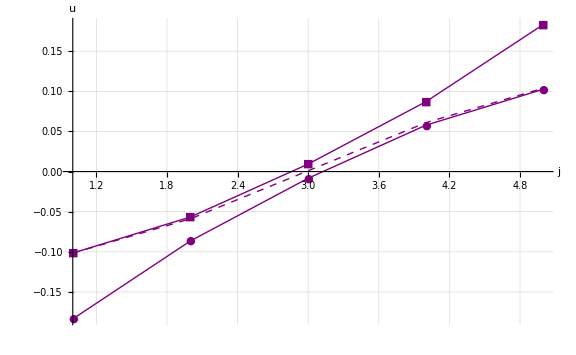

```mathematica
AveragePositionCollagenDataPlot=Table[
ListLinePlot[
{
xData[[i]][[4]],
yData[[i]][[4]],
zData[[i]][[4]]
},
PlotRange->All,
AxesOrigin->{1,0},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["u",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Purple},
{Thick,Dashed,Purple},
{Thick,Purple}
},
PlotMarkers->{"●","","■"},
PlotLegend->{
Style["x_j",FontSize->fs2],
Style["y_j",FontSize->fs2],
Style["z_j",FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.5,0.3},
LegendPosition->{0.4,-0.5}
]
,{i,1,3}
];
AveragePositionCollagenDataPlot
```

```mathematica
Export["./col_avg_har_delta3_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[1]]];
Export["./col_avg_hard_soft_delta3_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[2]]];
Export["./col_avg_soft_hard_delta3_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[3]]];
```

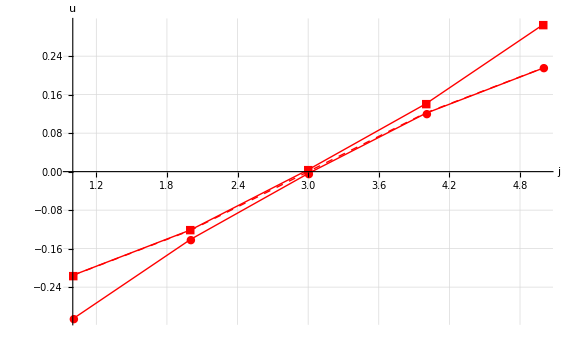
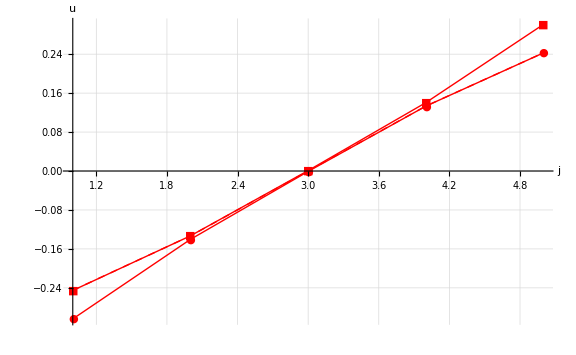
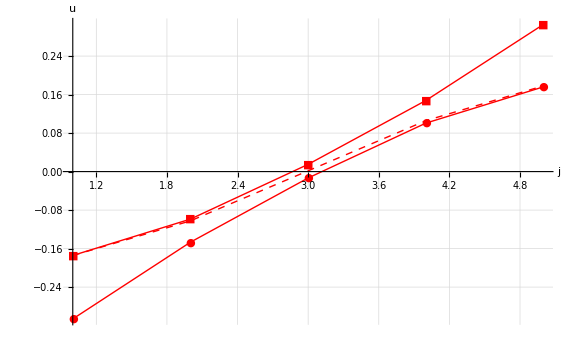

```mathematica
AveragePositionCollagenDataPlot=Table[
ListLinePlot[
{
xData[[i]][[6]],
yData[[i]][[6]],
zData[[i]][[6]]
},
PlotRange->All,
AxesOrigin->{1,0},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["u",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Red},
{Thick,Dashed,Red},
{Thick,Red}
},
PlotMarkers->{"●","","■"},
PlotLegend->{
Style["x_j",FontSize->fs2],
Style["y_j",FontSize->fs2],
Style["z_j",FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.65,0.3},
LegendPosition->{0.2,-0.5}
]
,{i,1,3}
];
AveragePositionCollagenDataPlot
```

```mathematica
Export["./col_avg_har_delta5_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[1]]];
Export["./col_avg_hard_soft_delta5_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[2]]];
Export["./col_avg_soft_hard_delta5_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",AveragePositionCollagenDataPlot[[3]]];
```